```mathematica
FF[n_, r_] := Sum[FractionalPart[n/x],{x,r,n}]
```

```mathematica
FF[100,51]
```

13119434949299548336211704572006746344217/697203752297124771645338089353123035568

```mathematica
FF2[n_, r_] := Sum[1-((x-r)/(n-r)),{x,r,n}]
```

```mathematica
FF2[100,50]
```

51/2

```mathematica
N[0/50]
```

0.

```mathematica
N[FractionalPart[100/51]]
```

0.960784

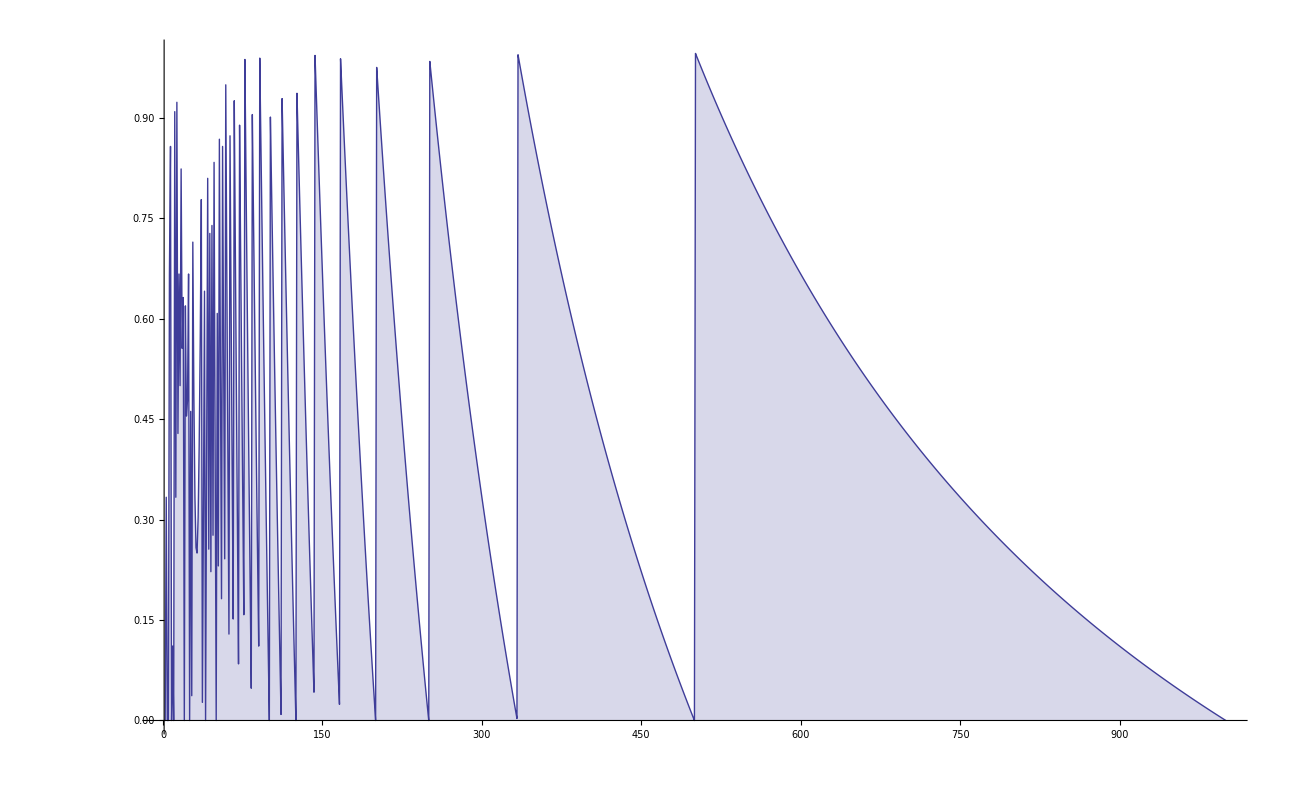

```mathematica
DiscretePlot[ FractionalPart[1000/n],{n,1,1000}]
```

```mathematica
Sum[FractionalPart[n/x],{x,Floor[n/2]+1,n}]
```

-n+Floor[n/2]+n PolyGamma[0,1+n]-n PolyGamma[0,1+Floor[n/2]]

```mathematica
Sum[FractionalPart[n/x],{x,Floor[n/3]+1,n/2}]
```

-n+2 Floor[n/3]+n PolyGamma[0,1+n/2]-n PolyGamma[0,1+Floor[n/3]]

```mathematica
FF[100,51]
```

13119434949299548336211704572006746344217/697203752297124771645338089353123035568

```mathematica
FP[n_,a_] :=Sum[FractionalPart[n/x],{x,Floor[n/(a+1)]+1,n/a}]
```

```mathematica
FP[100,1]
```

13119434949299548336211704572006746344217/697203752297124771645338089353123035568

```mathematica
FF[99,50]
```

2692903118875180604233495593953476599637/140849242888308034675825876636994552640

```mathematica
FP[99]
```

2692903118875180604233495593953476599637/140849242888308034675825876636994552640

```mathematica
FF2[n_,a_] := FF[n,Floor[n/(a+1)]+1, n/a]
```

```mathematica
FF[100,51,100]
```

13119434949299548336211704572006746344217/697203752297124771645338089353123035568

```mathematica
FF[n_, r1_,r2_] := Sum[FractionalPart[n/x],{x,r1,r2}]
FP[n_,a_] :=Sum[FractionalPart[n/x],{x,Floor[n/(a+1)]+1,n/a}]
Table[ FP[100,n]-FF2[100,n],{n,1,99}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FF2[n,a]
```

∑_(x=1+Floor[n/(1+a)])^(n/a) FractionalPart[n/x]

```mathematica
FP[n,a]
```

∑_(x=1+Floor[n/(1+a)])^(n/a) FractionalPart[n/x]

```mathematica
Sum[FractionalPart[n/x],{x,Floor[n/(3+1)]+1,n/3}]
```

-n+3 Floor[n/4]+n PolyGamma[0,1+n/3]-n PolyGamma[0,1+Floor[n/4]]

```mathematica
Sum[FractionalPart[n/x],{x,Floor[n/(4+1)]+1,Floor[n/4]}]
```

∑_(x=1+Floor[n/5])^Floor[n/4] FractionalPart[n/x]

```mathematica
FR[n_, a_] := -n+a Floor[n/(a+1)]+n PolyGamma[0,1+n/a]-n PolyGamma[0,1+Floor[n/(a+1)]]-(n/a-Floor[n/a])
```

```mathematica
N[FR[100,3]]
```

2.94071

```mathematica
N[FP[100,3]]
```

3.284